```mathematica
Play[Sin[300 t Sin[10 t]]/(1+t),{t,0,5}]
```

-Graphics-

```mathematica
Graphics[List[RGBColor[1,0,0],Disk[List[0,0],2]]]
```

-Graphics-

```mathematica
TreeForm[%]
```

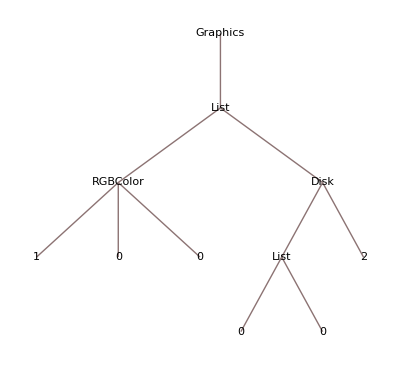

```mathematica
-Graphics-/.Disk[{x_,y_},r_] -> Disk[{x,y},{0.8 r,0.35 r}]
```

-Graphics-

```mathematica
mousepos = Dynamic[MousePosition[]]
```

```mathematica
elisse=-Graphics-/.Disk[{x_,y_},r_] -> Disk[{x,y},mousepos ]
```

-Graphics-

```mathematica
Manipulate[Plot[Sin[n x],{x,0,10}],{n,1,10}]
```

```mathematica
DynamicModule[{n=10.},Plot[Sin[n x],{x,0,10}]]
```

```mathematica
TabView[{1-> "一",2-> "二",3-> "三"}]
```

123

```mathematica
face=Graphics[{Yellow,Disk[{0,0},10],White,Disk[{4,4},2],Disk[{-4,4},2],Black,
Disk[
Dynamic[
(MousePosition["Graphics",{4,4}]-{4,4})*0.1+{4,4}],1],
Disk[
Dynamic[
(MousePosition["Graphics",{-4,4}]-{-4,4})*0.1+{-4,4}],1]
}]
```

-Graphics-

```mathematica
Expand[(elisse+face)^2];
```

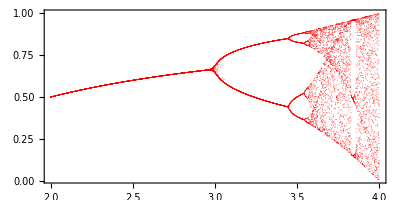

```mathematica
Graphics[{PointSize[0.001],Red,
Point[Table[{r,Nest[(r # (1. - #))&,Random[],100]},
{r,2,4,0.0001}]]},Frame-> True,FrameTicks->True]
```

```mathematica
Manipulate[

Plot3D[
100/((x-1)^2+(y-1)^2+1)- 100/((x+1)^2+(y+2)^2+1),
{x,-3,2},
{y,-3,2},
PlotPoints->25,
ColorFunction-> ({
Specularity[gloss],
Opacity[opa],
Blend[name,xdir #1+ydir #2+zdir #3]}&),
Mesh->None],
{name,ColorData["Gradients"]},
{{xdir,0},0,1},
   {{ydir,0},0,1},
   {{zdir,1},0,1},
   {gloss,0,1},
   {{opa,1},0,1}
]
```

```mathematica
Table[Plot3D[Abs[f[x+I y]],{x,-2,2},{y,-2,2},
MeshFunctions-> {#3 &},
MeshStyle->None,
MeshShading -> {None,Green,None,Yellow},
PlotLabel-> f,
Ticks-> None],
{f,{Cos,Tan,Cot}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ContourPlot3D[x^2+y^2-(1-z) z^4 ==0.0,
{x,-1,1},
{y,-1,1},
{z,-1,1.001},
RegionFunction->(#1^2+#2^2<1 &),
PlotPoints->65,
MaxRecursion->2,
ContourStyle->{Specularity[White,50],
RGBColor[0.15686274509,0.454901960784,0.9490196078]}]
```

```mathematica
s=Table[i+j,{i,1,3},{j,1,3}];
```

```mathematica
ss=MatrixForm[%]
```

```mathematica
data=RandomReal[NormalDistribution[],{300,2}];
data=Apply[{#1,#2,Exp[-#1^2-#2^2]}&,data,{1}];
points=Graphics3D[Map[Point,data],Axes->True]
```

-Graphics3D-

```mathematica
Manipulate[ListPlot3D[data,PlotRange->All,ColorFunction->clr],{clr,ColorData["Gradients"]}]
```

```mathematica
Dynamic[xx]
```

```mathematica
xx=10
```

10

```mathematica
Slider[Dynamic[xx]]
```

```mathematica
Slider[Dynamic[1-xx]]
```

```mathematica
PopupMenu[
Dynamic[nodes],
Table[i->i,{i,100}],
1,
Dynamic[GraphPlot[Table[i-> Mod[i^2,nodes],
{i,0,nodes}]]]]
```